```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
allElemData=Take[#[EntityProperty["Element","AtomicSymbol"]]->#[EntityProperty["Element","Resistivity"]]&/@EntityList@EntityClass["Element",All]//Association//Sort//DeleteMissing,{1,-10}]//Dataset
```

```mathematica
(QuantityMagnitude[#])&@@@(allElemData//Normal)//KeyValueMap[List,#]&;
%//Export["~/Downloads/elemRests.csv",#]&
```

~/Downloads/elemRests.csv

## Measurements of the setup

```mathematica
L=10^-2{10,40,60}&/@Range[1,6]//N; (* Lengths of the wires (cm) *)
r=1/2 10^-3{1.00,0.74,0.71,0.51,0.35,0.52}; (* Radii of the wires (mm) *)
```

## 2-probes measurement of resistivity

```mathematica
V=10^-3{{0.381,0.515,0.62},{0.52,0.756,1.015},{0.5,0.763,1.026},{0.774,1.302,1.838},{1.29,2.338,3.378},{0.382,0.44,0.524}};
```

```mathematica
fnfit=LinearModelFit[Transpose[#],x,x]&/@Transpose[{L,V}];
```

```mathematica
Plot[#["BestFit"]&/@fnfit//Evaluate,{x,0,1},PlotLabels->"Expressions",ImageSize->Large]//Show[#,ListPlot[Transpose[#]&/@Transpose[{L,V}]]]&
```

-Graphics-

```mathematica
slopes=#["BestFitParameters"][[2]]&/@fnfit
```

{0.000475526,0.000973947,0.00103816,0.00209895,0.00412211,0.000276842}

```mathematica
rests=#1(π#2^2)/10^-3&@@@Transpose[{slopes,r}];
```

```mathematica
samples=CharacterRange["A","F"];
means=#1->#2 Quantity[, "Meters" "Ohms"]&@@@Transpose[{samples,rests}]//Association//Dataset
```

```mathematica
ListPlot[{means,allElemData},PlotRange->Automatic,ImageSize->Large,PlotLabel->"2-probes aquisition method"]
```

-Graphics-

```mathematica
Nearest[allElemData//Normal,#,10]&/@Values[means]//Normal//#1->#2&@@@Transpose[{samples,#}]&//Association//Dataset
```

## 4-probes measurement of resistivity

```mathematica
V=10^-3{{0.05,0.212,0.335},{0.18,0.45,0.711},{0.193,0.44,0.712},{0.453,0.969,1.5},{0.970,2.02,3.063},{0.008,0.08,0.18}};
```

```mathematica
fnFit=LinearModelFit[Transpose[#],x,x]&/@Transpose[{L,V}];
```

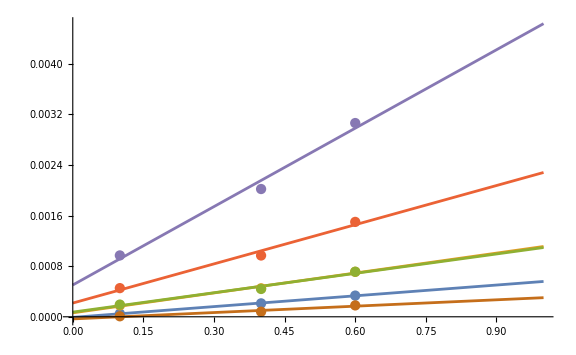

```mathematica
Plot[#["BestFit"]&/@fnFit//Evaluate,{x,0,1},ImageSize->Large,PlotRange->All]//Show[#,ListPlot[Transpose[#]&/@Transpose[{L,V}]],PlotRange->All]&
```

```mathematica
slope=#["BestFitParameters"][[2]]&/@fnFit;
```

```mathematica
rests=#1(π#2^2)/10^-3&@@@Transpose[{slope,r}];
means=#1->#2 Quantity[, "Meters" "Ohms"]&@@@Transpose[{samples,rests}]//Association//Dataset
```

```mathematica
ListPlot[{means,allElemData},PlotRange->Automatic,ImageSize->Large,PlotLabel->"4-probes aquisition method"]
```

-Graphics-

```mathematica
Nearest[allElemData//Normal,#,10]&/@Values[means]//Normal//#1->#2&@@@Transpose[{samples,#}]&//Association//Dataset
```

## First part of the experiment with the thermistor

```mathematica
data=Import["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/RT/Dati.txt","Table","HeaderLines"->6,"FieldSeparators"->"\t","NumberPoint"->",",CharacterEncoding->"UTF8"]//Dataset//#[All,Range[1,12]]&;
data=data[All,<|"t (s)"->1,"V_1 (V)"->2,"V_2 (V)"->3,"V_3 (V)"->4,"V_4 (V)"->5,"R_1 (Ω)"->6,"R_2 (Ω)"->7,"R_3 (Ω)"->8,"T (K)"->9,"R_1/(R_(1, 0))"->10,"R_2/(R_(2, 0))"->11,"R_3/(R_(3, 0))"->12|>]
```

Dataset[<>]

```mathematica
With[{retr={"R_1/(R_(1, 0))","R_2/(R_(2, 0))","R_3/(R_(3, 0))"}},ListLinePlot[Transpose[{data[All,"T (K)"],data[All,#]}//Normal]&/@retr,PlotRange->All,PlotLabels->retr,AxesLabel->{"T (K)","R (Ω)"}]]
```

-Graphics-

```mathematica
With[{retr={"R_1/(R_(1, 0))","R_2/(R_(2, 0))","R_3/(R_(3, 0))"}},ListLinePlot[Transpose[{data[All,"t (s)"],data[All,#]}//Normal]&/@retr,PlotRange->All,PlotLabels->retr,AxesLabel->{"t (s)"}]]
```

-Graphics-

```mathematica
With[{retr={"V_1 (V)","V_2 (V)","V_3 (V)","V_4 (V)"}},ListLinePlot[Transpose[{data[All,"t (s)"],data[All,#]}//Normal]&/@retr,PlotRange->All,PlotLabels->retr,AxesLabel->{"t (s)","V (V)"}]]
```

-Graphics-

```mathematica
z
```

z